```mathematica
input:=Import["/home/andrew/ParticleSim/velocities.dat","Table"]
```

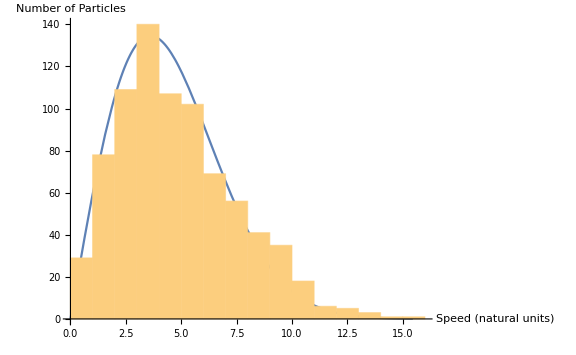

```mathematica
speeds:=Map[Function[row,√(row[[1]]^2+row[[2]]^2)],input]
Subscript[k, b]=1;m=1;NParticles=800;
f[v_,T_]:=2π v * m/(2 π Subscript[k, b] T)Exp[-(m v^2)/(2 Subscript[k, b] T)]
w=1;T=13;
Show[
Plot[NParticles*w*f[v,T],{v,0,Max[speeds]}],
Histogram[speeds,{w}],
AxesLabel->{HoldForm[Speed (natural units)],HoldForm[Number of Particles]},
LabelStyle->{14,RGBColor[0.,0.,0.]},
ImageSize-> Large,
PlotRange-> All
]
```